### 2 D Problem

```mathematica
{egnVal,egnVec}=NDEigensystem[
{(-1/2)* Laplacian[R2D[x,y],{x,y},"Cartesian"],
(*DirichletCondition[R2D[x,y]==0,x==0 || x==10 || y==0 || y==10]},*)
PeriodicBoundaryCondition[R2D[x,y],x==0,TranslationTransform[{10,0}]],
PeriodicBoundaryCondition[R2D[x,y],y==0,TranslationTransform[{0,10}]]},
R2D[x,y],{x,0,  10},{y,0,10},13, Method -> {"Eigensystem" ->"Direct"} ];
ord =Ordering[egnVal];
Sort[egnVal]
```

{0.,0.197395,0.197395,0.197395,0.197395,0.39479,0.39479,0.39479,0.39479,0.789736,0.789736,0.789736,0.789736}

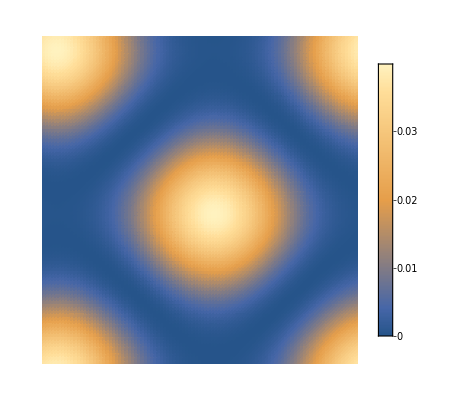

```mathematica
F1 =Part[Re[egnVec],Part[ord,3]]^2;
DensityPlot[F1,{x,0,10},{y,0,10}, PlotTheme->"Minimal",  PlotPoints->100, PlotRange->All, PlotLegends->Automatic]
(*Export[NotebookDirectory[]<>"5.png",%,ImageResolution->100];*)
```

```mathematica
ParametricPlot3D[{r Cos[θ],r Sin[θ],1000*Evaluate[F1]},{r,0,rMax*Sqrt[2]},{θ,0,2 π}, PlotTheme->"Minimal", PlotPoints->100]
```